```mathematica
(*For the purpose of benchmark, this notebook solves a simple model of ϕ^4-inflation*)
```

### Define theory

#### Parameters

```mathematica
λ0=1*^-9;
```

#### Potential

```mathematica
U[χ_]= 1/4 λ0 χ^4 ;
```

#### Derived functions

```mathematica
dU[χ_]= D[U[χ],χ];
ϵSR[χ_]= 1/2(dU[χ]/U[χ])^2;
```

```mathematica
ηSR[χ_]=D[dU[χ],χ]/U[χ];
```

## Solve background e.o.m.

#### Initial conditions

```mathematica
χi = 70.
```

70.

```mathematica
dχi = -Sqrt[2ϵSR[χi]]
```

-0.0571429

#### Numerical solution

```mathematica
L =1000;
```

```mathematica
χsol =NDSolveValue[{y''[Ne] + 3 y'[Ne] -1/2 (y'[Ne])^3 + (3-1/2(y'[Ne])^2)dU[y[Ne]]/U[y[Ne]]==0,y[0]==χi, y'[0]==dχi},y,{Ne,$MachineEpsilon,L}]
```

NDSolveValue::ndsz: At Ne == 614.643, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

Here Ne increases as function of time (in contrast to standard convention)

#### Find end of inflation

Exact slow-roll parameter

```mathematica
ϵ[x_]= 1/2(χsol'[x])^2;
```

```mathematica
η[x_] =ϵ[x] - 0.5 ϵ'[x]/ϵ[x];
```

```mathematica
(*Slow-roll η *)
```

```mathematica
ηSR2[x_] = ϵ[x]+η[x];
```

```mathematica
Nend = 0; While[ϵ[Nend]<1&&Nend<L,Nend = Nend+0.1]
```

```mathematica
Nend
```

613.

```mathematica
NCMB=Nend-55;
```

#### Plot

Plot solution (field value as function of number of e-foldings)

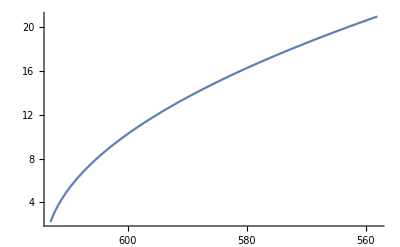

```mathematica
Plot[χsol[Ne],{Ne,NCMB,Nend},ScalingFunctions->{"Reverse",Identity}]
```

Plot slow-roll parameters

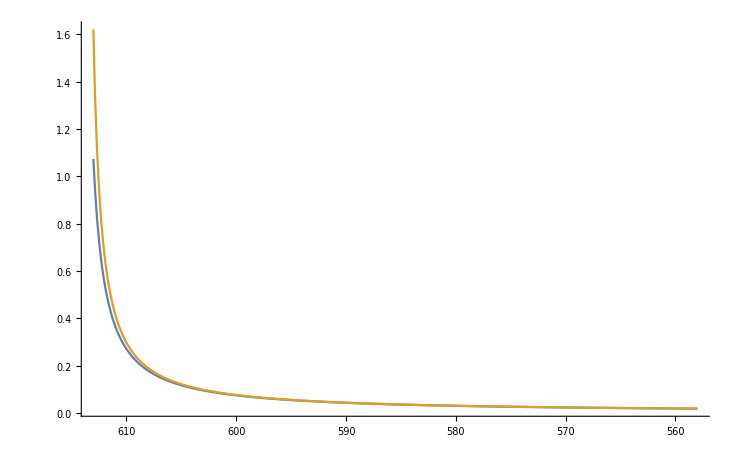

```mathematica
Plot[{ϵ[Ne],ϵSR[χsol[Ne]]},{Ne,NCMB,Nend},ScalingFunctions->{"Reverse",Identity},PlotRange->All]
```

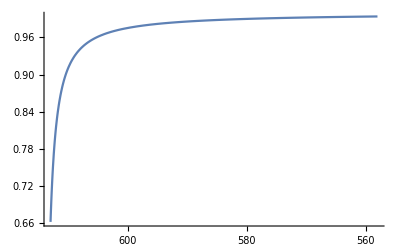

```mathematica
Plot[ϵ[Ne]/ϵSR[χsol[Ne]],{Ne,NCMB,Nend},ScalingFunctions->{"Reverse",Identity},PlotRange->All]
```

```mathematica
{ϵ[NCMB],ϵSR[χsol[NCMB]]}
```

{0.0181048,0.0182146}

ϵ agree, as they should

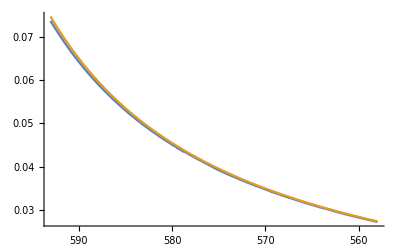

```mathematica
Plot[{ηSR2[Ne],ηSR[χsol[Ne]]},{Ne,NCMB,Nend-20},ScalingFunctions->{"Reverse",Identity},PlotRange->All]
```

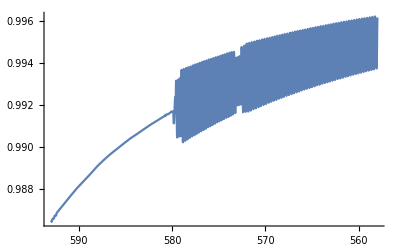

```mathematica
Plot[ηSR2[Ne]/ηSR[χsol[Ne]],{Ne,NCMB,Nend-20},ScalingFunctions->{"Reverse",Identity},PlotRange->All]
```

```mathematica
{ηSR2[NCMB],ηSR[χsol[NCMB]]}
```

{0.0272166,0.0273218}

Show potential and which part of it is explored

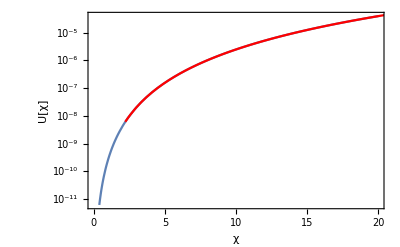

```mathematica
p1 = LogPlot[U[x],{x,0,20},Frame->True,FrameLabel->{χ,"U[χ]"},FrameStyle->Black];
p2 = LogPlot[U[x],{x,χsol[NCMB],χsol[Nend]},PlotStyle->Red];
Show[p1,p2]
```

## Calculate perturbations

#### Plug exact background solution in slow-roll formula

```mathematica
H[x_]=Sqrt[2 U[χsol[x]]/(6-(χsol'[x])^2)];
Pζ[Nfold_]= H[Nfold]^2/(8 Pi^2 ϵ[Nfold]);
```

#### Now do exact computation

```mathematica
TMukh = {};(* Empty List*)
TMukhValue = {};
Mp=2.4 10^18;(*GeV*)
HMpc[x1_] = H[x1] Mp 1.56 10^38; (*Mpc^-1*);
kcom[Ne1_]= (0.05 H[Ne1])/H[NCMB] E^(Ne1-NCMB);
Ne= Interpolation[Table[{kcom[x],x},{x,NCMB-5,Nend,0.01}]];
ascale[x1_] =(0.05 (*Mpc^-1*)/( HMpc[NCMB](*Mpc^-1*))) Exp[x1-NCMB];
Foo[x1_,k1_] = (k1/(kcom[x1]))^2+(1+ϵ[x1] - η[x1])(η[x1]-2)-(ϵ'[x1]-η'[x1]); 
M = 100; (*Number of Points*)
For[k=kcom[NCMB],k<=kcom[Nend],k= k (kcom[Nend]/kcom[NCMB])^(1/M),
(*we go far in the horizon for the intial condition*)
ki=k /10;
If[Ne[k]+3<Nend, Nf = Ne[k]+3, Nf = Nend];
Ni = Ne[ki];
(*Scaling improves stability of NDSolveValue *)
scaling = 10^5;
RuinScaled =1/scaling; dRuinScaled = 0;(*Real Part of Bunch Davies Vacuum*)
RusolScaled = NDSolveValue[{(f''[x]+ (1-ϵ[x])f'[x]+(Foo[x,k])f[x])==0,f[Ni]==RuinScaled,f'[Ni]==dRuinScaled},f,{x,Ni,Nf}];
IuinScaled = 0; dIuinScaled = -k/ki/scaling;(*Imaginary part of Bunch Davies Vacuum*)
IusolScaled = NDSolveValue[{(f''[x]+ (1-ϵ[x])f'[x]+(Foo[x,k])f[x])==0,f[Ni]==IuinScaled,f'[Ni]==dIuinScaled},f,{x,Ni,Nf}];
(*Now here normalization is added*)
uSquared =scaling^2/(2k)( RusolScaled[Nf]^2 +IusolScaled[Nf]^2);(*Mpc, since we set the initial condition as fct of k in Mpc*)
z = -ascale[Nf]χsol'[Nf] Mp 1.56 10^38; (*Mpc^-1, the numerical factor is the conversion factor btw Mpc^-1 and GeV.*)
Pow = k^3 uSquared/((2π^2)z^2);(*Dimensionless*)
AppendTo[TMukh,{k,Pow}];
AppendTo[TMukhValue,{Pow}];]
```

#### Compare the results

```mathematica
q1 = ListLogLogPlot[TMukh,PlotStyle->Orange,Joined->True];
q2 = LogLogPlot[Pζ[Ne[x]],{x,kcom[NCMB],kcom[Nend]},PlotRange->All,Frame->True,FrameLabel->{"k["Superscript["Mpc]",-1],Subscript[P,R]["k"]},FrameStyle->Black];
```

Orange is exact and blue is approximation

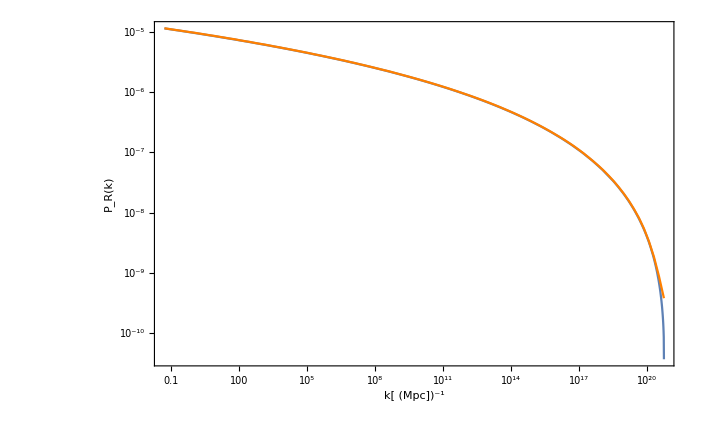

```mathematica
Show[q2,q1]
```

#### At CMB

```mathematica
Interpolation[TMukh][kcom[NCMB]]
```

0.0000113722

```mathematica
Pζ[NCMB]
```

0.0000113137

```mathematica
U[χsol[NCMB]]/ϵSR[χsol[NCMB]]/(24 Pi^2)
```

0.0000111777

All matches